# Hall Voltage, Magnetic Field and NMR frequency for H_2 O

```mathematica
H[VH_]:=1/9.27 VH 0.1
```

```mathematica
L={{12.4,30.215},
{12.6,30.708},
{12.8,31.200},
{13.0,31.690},
{13.2,32.185},
{13.4,32.678}};
```

```mathematica
J=LinearModelFit[L,x,x]
```

FittedModel[-0.317486+2.46229 x]

```mathematica
VH[ωNMR_]:=J[ωNMR]
```

```mathematica
VH[12.8]
```

31.1998

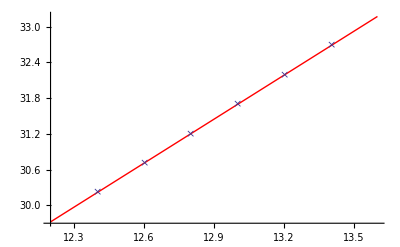

```mathematica
Show[Plot[Normal[J],{x,12.2,13.6},PlotStyle->Red],
ListPlot[L,PlotMarkers->{"×",Large}]]
```

```mathematica
H[VH[ωNMR]]//Simplify
```

-0.00342487+0.0265619 ωNMR

```mathematica
H[VH[12.8]]
```

0.336567

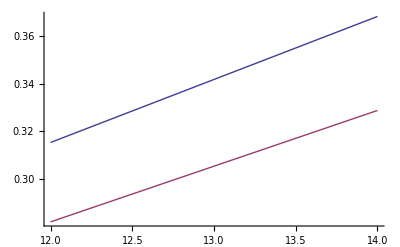

```mathematica
Plot[{H[VH[ωNMR]],ωNMR/42.5775} ,{ωNMR,12,14}]
```

```mathematica
Table[{H[VH[ωNMR]],VH[ωNMR],ωNMR},{ωNMR,12,14,0.2}];
%//TableForm
```

0.315318 | 29.2299 | 12.
0.32063 | 29.7224 | 12.2
0.325942 | 30.2149 | 12.4
0.331255 | 30.7073 | 12.6
0.336567 | 31.1998 | 12.8
0.341879 | 31.6922 | 13.
0.347192 | 32.1847 | 13.2
0.352504 | 32.6771 | 13.4
0.357817 | 33.1696 | 13.6
0.363129 | 33.6621 | 13.8
0.368441 | 34.1545 | 14.

```mathematica
(* theory*)
ωNMR=γp H
```

```mathematica
γp=42.5775
```

42.5775

```mathematica
1/42.5775
```

0.0234866